## To Do & Notes

## Global Path Configure

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Network Project/compareFS_v0.1/NDN-EB-algo/result201578

## Read in Data

```mathematica
fileName = "4-best-expbf-cs-rate-trace.txt";
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
n = Length[data]
data2 = Table[StringSplit[row,"\t"],{row,data}];
head = data2⟦1⟧;
entries = data2⟦2;;n⟧;
head
entries⟦1;;5⟧
```

35033

{Time,Node,FaceId,FaceDescr,Type,Packets,Kilobytes,PacketRaw,KilobytesRaw}

{{1,A,257,netDeviceFace://,InInterests,3012.8,67.5234,3766,84.4043},{1,A,257,netDeviceFace://,OutInterests,3807.2,85.3313,4759,106.664},{1,A,257,netDeviceFace://,InData,784,810.703,980,1013.38},{1,A,257,netDeviceFace://,OutData,411.2,425.195,514,531.494},{1,A,257,netDeviceFace://,InSatisfiedInterests,492.8,0,616,0}}

## Data Preprocessing

```mathematica
(*0号节点对应consumer*)
consumerEntries = Select[entries,StringMatchQ[#⟦2⟧,"BB"] &];
(*找到根据节点id把consumer节点分类，本topo中因为只有一个consumer所以差别不大，但是考虑到后面代码的兼容性，还是加这一行*)
consumer = GatherBy[consumerEntries,#⟦2⟧&];
consumer;
(*找出consumer节点集合中第一个consumer，读出其中Type为一下四类的entries*) 
tmp = Table[Select[consumer⟦1⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&],
{t,{"InInterests","InData","OutInterests","OutData"}}];
(*读出符合条件的entires中的times和Kilobytes信息*)
times = Table[Interpreter["Number"][ele⟦1⟧],{ele,tmp⟦1⟧}];
inInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦1⟧}];
inData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦2⟧}];
outInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦3⟧}];
outData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦4⟧}];
(*对多个不同的Type处理*)
(*把time和Kilboytes关联起来，然后把相同times下的list聚集起来*)
n = Length[times];
test = Table[
GatherBy[Table[{times⟦i⟧, t⟦i⟧},{i,1,n}],First],
{t,{inInterests,inData,outInterests,outData}}
];
(*形成时间序列数据*)
(*TimeSeries的好处是方便用ML的技巧拟合模型*)
tsdata= Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,test⟦i⟧}
],{i,1,4}
];
```

## Visualization

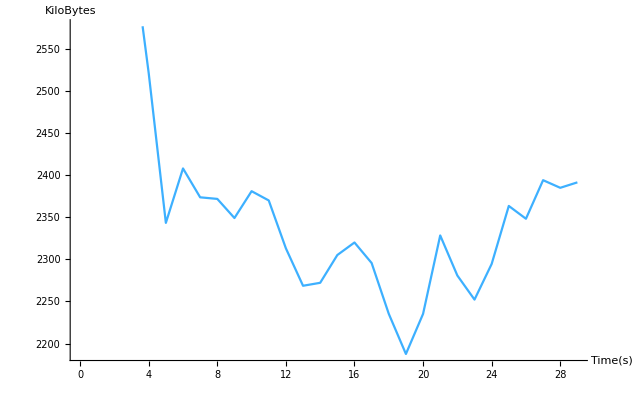

```mathematica
(*四个属性全部画在一起，会发现InInterest和OutInterest完全重合, InData和OutData全部重合，所以看上去只有二根线*)
ListPlot[
TimeSeries[tsdata⟦2⟧],
AxesLabel->{"Time(s)","KiloBytes"},
PlotStyle->96,
Joined->True
]
```

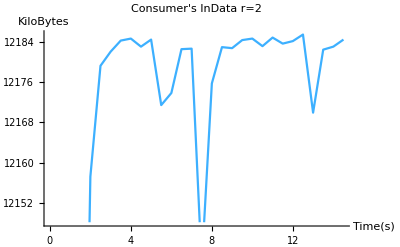

```mathematica
ListPlot[
TimeSeries[tsdata⟦2⟧],
PlotLabel-> "Consumer's InData r=2",
AxesLabel->{"Time(s)","KiloBytes"},
PlotLegends->"InData",
PlotStyle->96,
Joined->True
]
```

## Data Pre-processing for all nodes (Updata 2015-7-8)

### Step 1 : Gobal Define / Extraction and Aggregation

```mathematica
producerNodes = {"GG"};
consumerNodes = {"BB","AA","LL","MM"};
routerNodes = {"G","B","A","L","M"};
numOfProducers = Length[producerNodes];
numOfConsumers = Length[consumerNodes];
numOfRouters = Length[routerNodes];

(*先找出三类节点(producer,consumer,router),再在每类节点中根据节点id把节点聚类*)
producerEntries = Select[entries,MemberQ[producerNodes,#⟦2⟧] &];
producers = GatherBy[producerEntries,#⟦2⟧&];
producers;

consumerEntries = Select[entries,MemberQ[consumerNodes,#⟦2⟧] &];
consumers = GatherBy[consumerEntries,#⟦2⟧&];
consumers;

routerEntries = Select[entries,MemberQ[routerNodes,#⟦2⟧] &];
routers = GatherBy[routerEntries,#⟦2⟧&];
routers;
```

### Step 2: Key Information Read Out

```mathematica
(*读出符合条件的entires中的times和Kilobytes信息*)
tmpProducers = Table[
Table[Select[producers⟦i⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&
],
{t,{"InInterests","InData","OutInterests","OutData"}}
],
{i,1,numOfProducers}
];
tmpConsumers = Table[
Table[Select[consumers⟦i⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&
],
{t,{"InInterests","InData","OutInterests","OutData"}}
],
{i,1,numOfConsumers}
];
tmpRouters = Table[
Table[Select[routers⟦i⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&
],
{t,{"InInterests","InData","OutInterests","OutData"}}
],
{i,1,numOfRouters}
];
```

### Step 3: Aggregate nodes’ Informations

```mathematica
(*Consumers*)
timesConsumers = Table[
Table[Interpreter["Number"][ele⟦1⟧],{ele,node⟦1⟧}],
{node,tmpConsumers}
];
inInterestsConsumers =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦1⟧}],
{node,tmpConsumers}
];
inDataConsumers =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦2⟧}],
{node,tmpConsumers}
];
outInterestsConsumers = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦3⟧}],
{node,tmpConsumers}
];
outDataConsumers = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦4⟧}],
{node,tmpConsumers}
];

(*Producers*)
timesProducers = Table[
Table[Interpreter["Number"][ele⟦1⟧],{ele,node⟦1⟧}],
{node,tmpProducers}
];
inInterestsProducers =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦1⟧}],
{node,tmpProducers}
];
inDataProducers =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦2⟧}],
{node,tmpProducers}
];
outInterestsProducers = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦3⟧}],
{node,tmpProducers}
];
outDataProducers = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦4⟧}],
{node,tmpProducers}
];

(*Routers*)
timesRouters = Table[
Table[Interpreter["Number"][ele⟦1⟧],{ele,node⟦1⟧}],
{node,tmpRouters}
];
inInterestsRouters =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦1⟧}],
{node,tmpRouters}
];
inDataRouters =  Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦2⟧}],
{node,tmpRouters}
];
outInterestsRouters = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦3⟧}],
{node,tmpRouters}
];
outDataRouters = Table[
Table[Interpreter["Number"][ele⟦7⟧],{ele,node⟦4⟧}],
{node,tmpRouters}
];
```

### Step 4: Transfer to Time Series

```mathematica
(*Consumers*)
testConsumers = Table[
Table[
GatherBy[Table[{timesConsumers⟦j⟧⟦i⟧, t⟦i⟧},{i,1,Length[timesConsumers⟦j⟧]}],First],
{t,{inInterestsConsumers⟦j⟧,inDataConsumers⟦j⟧,outInterestsConsumers⟦j⟧,outDataConsumers⟦j⟧}}
],
{j,1,numOfConsumers}
];
tsdataConsumers = Table[
Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,node⟦i⟧}
],{i,1,4}
],
{node,testConsumers}
];

(*Producers*)
testProducers= Table[
Table[
GatherBy[Table[{timesProducers⟦j⟧⟦i⟧, t⟦i⟧},{i,1,Length[timesProducers⟦j⟧]}],First],
{t,{inInterestsProducers⟦j⟧,inDataProducers⟦j⟧,outInterestsProducers⟦j⟧,outDataProducers⟦j⟧}}
],
{j,1,numOfProducers}
];
tsdataProducers = Table[
Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,node⟦i⟧}
],{i,1,4}
],
{node,testProducers}
];

(*Routers*)
testRouters= Table[
Table[
GatherBy[Table[{timesRouters⟦j⟧⟦i⟧, t⟦i⟧},{i,1,Length[timesRouters⟦j⟧]}],First],
{t,{inInterestsRouters⟦j⟧,inDataRouters⟦j⟧,outInterestsRouters⟦j⟧,outDataRouters⟦j⟧}}
],
{j,1,numOfRouters}
];
tsdataRouters = Table[
Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,node⟦i⟧}
],{i,1,4}
],
{node,testRouters}
];
```

### Step 5 (optional) debuging

```mathematica
a = tsdataConsumers⟦1⟧;
b = tsdataProducers⟦1⟧;
c = tsdataRouters⟦1⟧;
```

```mathematica
c
```

{{0.5→293.394,1→461.444,1.5→419.832,2→400.879,2.5→418.056,3→436.72,3.5→454.587,4→490.939,4.5→475.513,5→460.447,5.5→453.51,6→442.335,6.5→457.27,7→442.919,7.5→456.881,8→473.932,8.5→449.5,9→432.716,9.5→426.11,10→442.719,10.5→482.326,11→464.679,11.5→426.038,12→413.207,12.5→414.547,13→472.255,13.5→450.872,14→480.917,14.5→518.802},{0.5→6388.34,1→10903.,1.5→10644.3,2→10443.7,2.5→9536.48,3→6543.73,3.5→5293.24,4→4463.99,4.5→4341.16,5→4718.7,5.5→4999.38,6→5465.87,6.5→5458.24,7→4617.79,7.5→4170.05,8→4815.19,8.5→5081.56,9→4547.42,9.5→2845.47,10→3880.13,10.5→3740.64,11→3093.11,11.5→3691.1,12→3467.8,12.5→2444.04,13→3137.52,13.5→2435.57,14→2284.94,14.5→2549.29},{0.5→289.049,1→437.793,1.5→409.829,2→389.85,2.5→408.551,3→413.599,3.5→440.554,4→476.405,4.5→448.728,5→442.138,5.5→430.357,6→424.077,6.5→432.862,7→421.583,7.5→429.115,8→443.699,8.5→430.501,9→389.471,9.5→390.25,10→388.803,10.5→438.06,11→402.668,11.5→384.549,12→354.621,12.5→363.022,13→414.756,13.5→385.806,14→418.381,14.5→417.32},{0.5→6876.47,1→12195.3,1.5→10686.,2→10230.3,2.5→9080.13,3→6972.03,3.5→4986.74,4→4012.19,4.5→3770.95,5→3803.78,5.5→3836.83,6→4088.32,6.5→4112.14,7→3688.35,7.5→3633.37,8→4097.27,8.5→4006.39,9→3423.96,9.5→2572.79,10→2847.67,10.5→2903.71,11→2761.92,11.5→2852.12,12→2285.64,12.5→2056.98,13→2191.36,13.5→2016.23,14→1572.17,14.5→1882.07}}